```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,9.468,18.694,27.,32.96,34.86,34.48,33.42,32.58,32.28,32.66,33.64,34.9,35.64,34.4,29.520000000000003,22.64,15.09,7.506,0},{0,19.18,38.3,56.379999999999995,69.94,71.98,69.62,66.64,64.56,63.88,64.72,67.,70.3,73.28,72.42,61.06,45.9,30.220000000000002,14.934,0},{0,28.939999999999998,58.96,90.25999999999999,118.43999999999998,113.53999999999999,105.33999999999999,98.98,95.16,93.94,95.32000000000001,99.32,106.,114.74,120.9,96.44,69.72,44.96,22.,0},{0,37.66,78.3,127.3,200.,158.38,139.24,128.72,123.14,121.39999999999999,123.25999999999999,128.96,139.62,158.82,200.,134.04,91.53999999999999,57.879999999999995,28.139999999999997,0},{0,43.38,89.28,140.6,200.,180.72,164.5,153.5,147.26,145.26,147.32,153.64,164.68,180.88,200.,148.2,104.56,66.88,32.66,0},{0,46.62,94.8,145.88,200.,200.,184.5,173.54,167.1,165.01999999999998,167.14,173.6,184.58,200.,200.,154.18,111.60000000000001,72.39999999999999,35.6,0},{0,48.28,97.44,148.07999999999998,200.,200.,200.,189.02,182.58,180.54,182.6,189.06,200.,200.,200.,156.9,115.28,75.53999999999999,37.36,0},{0,49.059999999999995,98.61999999999999,149.,200.,200.,200.,200.,193.64,191.96,193.64,200.,200.,200.,200.,158.12,117.06,77.14,38.279999999999994,0},{0,49.3,99.,149.28,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,158.51999999999998,117.66000000000001,77.72,38.62,0},{0,49.16,98.78,149.12,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,158.32,117.36,77.44,38.46,0},{0,48.559999999999995,97.86,148.4,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,157.4,116.02,76.24,37.76,0},{0,47.22,95.72,146.62,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,155.24,113.1,73.74000000000001,36.38,0},{0,44.56,91.2,142.34,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,150.42,107.4,69.26,33.96,0},{0,39.839999999999996,82.19999999999999,131.51999999999998,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,200.,139.08,96.84,61.88,30.259999999999998,0},{0,32.6,66.25999999999999,101.54,135.94,148.98,154.54000000000002,157.06,158.20000000000002,158.58,158.34,157.4,155.24,150.44,139.08,109.04,79.,51.2,25.16,0},{0,24.3,48.68,72.46000000000001,93.2,105.46,112.08,115.52,117.17999999999999,117.74,117.39999999999999,116.04,113.12,107.42,96.84,79.,58.879999999999995,38.78,19.201999999999998,0},{0,15.959999999999999,31.66,46.44,58.96,67.56,72.82,75.78,77.28,77.8,77.48,76.25999999999999,73.76,69.26,61.9,51.2,38.78,25.82,12.864,0},{0,7.8759999999999994,15.548,22.66,28.660000000000004,33.019999999999996,35.82,37.5,38.36,38.66,38.48,37.78,36.38,33.98,30.259999999999998,25.16,19.201999999999998,12.864,6.432,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

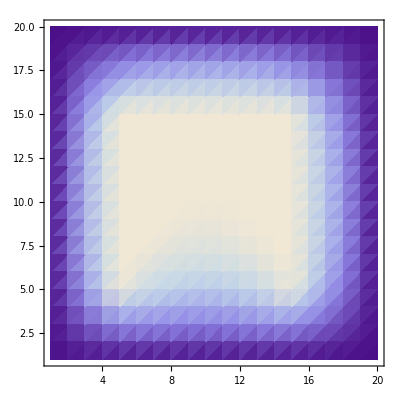

```mathematica
ListDensityPlot[data] (* Graf z barvno lestvico *)
```

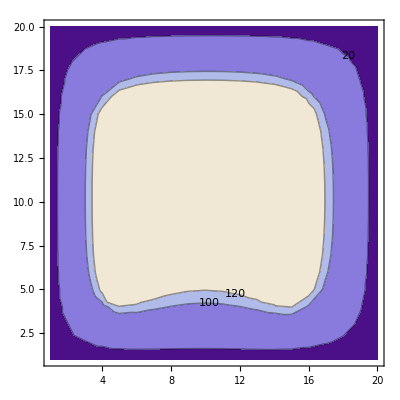

```mathematica
ListContourPlot[data,Contours->{20,100,120},ContourLabels->True] (* Izoterme + barve, lahko jih rocno dolocimo in oznacimo *)
```

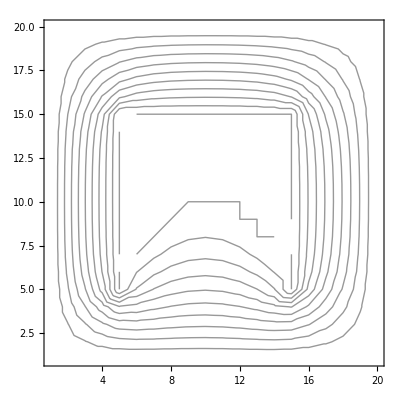

```mathematica
ListContourPlot[data, ContourShading->False] (* Le izoterme *)
(* Izgled dolocate s ContourStyle, ContourLabels - glej pomoc! *)
```

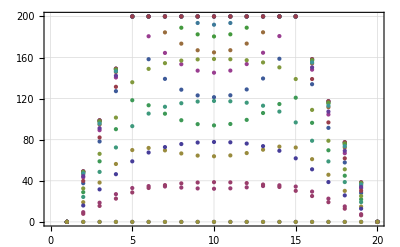

```mathematica
(* Skupni parametri grafov - preprosto naredimo seznam moznosti, ki ga vsem grafom dodamo na koncu - deluje direktno na ListPlot ali pa na Show *)
parametri={Frame->True,GridLines->Automatic,GridLinesStyle->Dashed};
ListPlot[data,parametri]
```

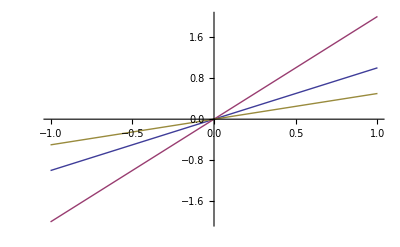

```mathematica
(* Vec krivulj/podatkov na ISTEM grafu *)
(* Vedno lahko v Plot/ListPlot dodate podatke kot seznam - samodejno obarvanje in podpora legende *)
plot1=Plot[{x,2x,x/2},{x,-1,1}]
```

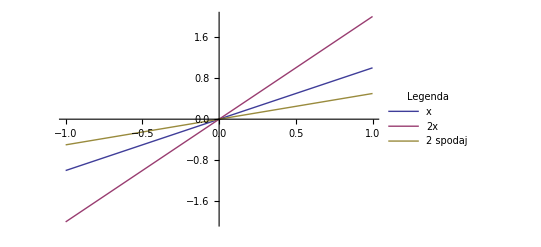

```mathematica
(* Legenda znotraj grafa - relativne koordinate glede na spodnji levi rob *)
(* Vec o legendah najdete v pomoci - LineLegend, PointLegend, BarLegend *)
legenda=Placed[LineLegend[{"x","2x","2 spodaj"},LegendFunction->Framed,LegendLabel->"Legenda"],{0.2, 0.75}];
plot2=Plot[{x,2x,x/2},{x,-1,1},PlotLegends->legenda]
```

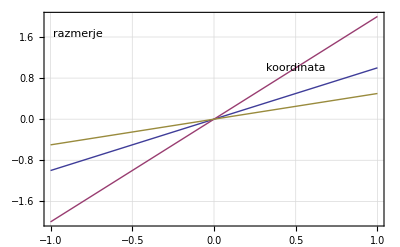

```mathematica
(* Oznaka grafa *)
(* Izris poljubnega teksta na doloceno KOORDINATO: *)
tekst1=Graphics[Text["koordinata",{0.5,1}]];
(* Izris poljubnega teksta na dolocen polozaj glede na razmerje velikosti grafa od 0-1: *)
tekst2=Graphics[Text["razmerje",Scaled[{0.1,0.9}]]];
(* Oznake dodamo s Show *)
Show[plot1,tekst1,tekst2,parametri]
```

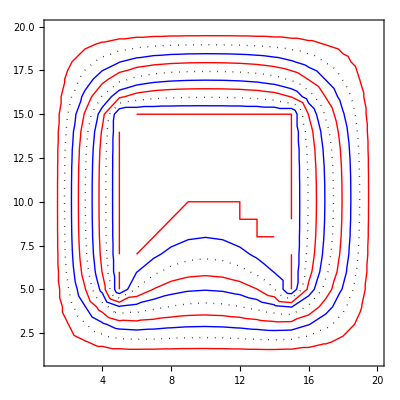

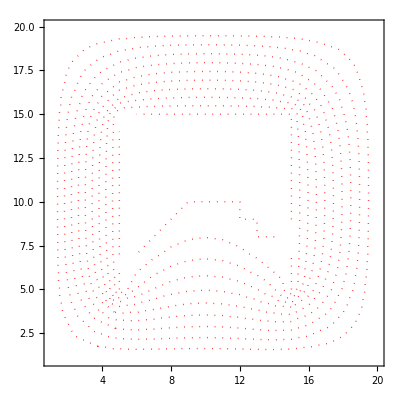

```mathematica
(* Nacini izbire izgleda *)
(* Zelimo alternirajoce oz. spremembe za vsako stvar posebej - seznam moznosti *)
ListContourPlot[data, ContourShading->False,ContourStyle->{Red,Dotted,Blue}]
(* Zelimo vec moznosti za VSE krivulje/crte - Directive[] *)
ListContourPlot[data, ContourShading->False,ContourStyle->Directive[Red,Dotted]]
```